# Arnoldi Dynamic Preconditioning

When run n times with a fixed m×m real matrix A and normalized m vector b the Arnoldi Process  generates a Tall Skinny Orthogonal m×(n+1) matrix Q_(n+1)and a rectangular (n+1)×n upper Hessenberg matrix H_n satisfying the update formula   
(R)	A.Q_(n+1)[All,1:n]=Q_(n+1).H_n=Q_n  with (Q_(n+1))ᵀ Q_(n+1)=I_(n+1)  
TSO and H are appropriate abbreviations.

The Arnoldi algorithm approximates eigenvalues of A with eigenvalues of the n×n upper Hessenberg matrix 
	H[1:n,1:n]
Under appropriate conditions eigenvalues of this upper Hessenberg matrix (called Ritz values) converge to eigenvalues on the outside edge of σ(A). The aim is to modify this process to approximate eigenvalues of A near a fixed complex conjugate pair α±ⅈ β while staying entirely in real arithmetic.

The plan is to modify a standard Krylov updating code 
(Arnoldi)	A:{Q_(n+1),H_n}->{Q_(n+2),H_(n+1)} 
to use a dynamically preconditioned matrix
(Precon)	 (μ I -B_n)^-1.A.((μ I - B_n)^*)^-1
where μ is a target eigenvalue and B_n is the current best estimate for A from the current Krylov space. 
	B_n=Q_(n+1)H_n Q_n^*∼A
This shift (Precon) should enhance eigen directions for eigenvalues near 
	μ=α+ⅈ β  and μ̄=α - ⅈ β
while preserving as much symmetry as possible.

Dynamically updating the matrix breaks the recursion (R) and I need to think about if it should be restored.  I think there is probably more than one way to think about this. 
1) Since the modifications all happen within the prior Arnoldi space I can keep track of them and maintain a factorization of the form   
	A.Q_n=Q_(n+1).F_n
where F_n is now a full matrix.
2) I can not worry about it and and see if I get any new ideas. 
Here is the original “expand” and “orthogonalize” code.  It requires no modification.

```mathematica
Arnoldi[A_][{Q_,H_}]:= Module[{m,n,HNew,w,h,q},
{m,n}=Dimensions[Q];
HNew=ConstantArray[0,{n+1,n}];HNew⟦1;;n,1;;n-1⟧=H;
w=A.Q⟦All,n⟧;
Do[
q=Q⟦All,k⟧;
HNew⟦k,n⟧=q.w;
w=w-HNew⟦k,n⟧ q,
{k,1,n}];
HNew⟦n+1,n⟧=Norm[w];
w=w/HNew⟦n+1,n⟧;
{ArrayFlatten[({{Q, {w}ᵀ}})],HNew}
]

BuildTest[m_,{α_,β_,γ_}]:= Module[{A,i,j,k},
(* Builds a real mxm matrix with a cloud of eigenvalues *)
A=RandomReal[{-√(2/m),√(2/m)},{m,m}]; 
(* builds a complex conjugate pair and a single real eigenvalue *)
(* near α±β and γ *)
{i,j,k}= RandomSample[Range[1,m],3];
AExtra = ({{γ, 0, 0}, {0, α, β}, {0, -β, α}});A⟦{i,j,k},{i,j,k}⟧=AExtra;
A
]
```

```mathematica
?RandomSample
```

I am going to build out a starting space without using the planned pivots.  Here is a test with three designed exterior eigenvalues.

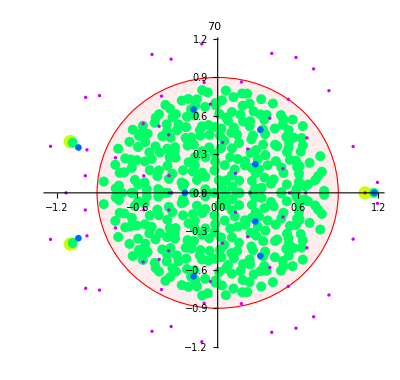

```mathematica
m=400;
{γ,α,β}={1.1,-1.1,0.4};
A=BuildTest[m,{α,β,γ}];
b=Normalize[RandomReal[{-1,1},m]];
{Q,H}={{b}ᵀ,{{}}};
n=10;
Do[
{Q,H}=Arnoldi[A][{Q,H}],
{n}]
μ=0.5;
B=μ IdentityMatrix[m]-Q.H.Q⟦All,1;;n⟧ᵀ;
BInv=Inverse[B];
EValPic=ListPlot[{
{{γ,0},{α,β},{α,-β}},
ReIm[Eigenvalues[A]],
ReIm[Eigenvalues[H⟦1;;n,1;;n⟧]],
ReIm[Hmm=Select[Eigenvalues[BInv.A.ConjugateTranspose[BInv]],Abs[#]<1.3&]]
},
PlotStyle->Table[Directive[PointSize[0.03(1-i/5)],Hue[i/5]],{i,1,5}],
PlotRange->All,
Prolog->{LightPink,EdgeForm[Red],Disk[{0,0},0.9]},
AspectRatio->Automatic,
PlotLabel->Length[Hmm]]
```